```mathematica
b=l/(p*(1-l)*(1-p*(1-l)))
```

l/((1-l) p (1-(1-l) p))

```mathematica
s1=l->(Exp[x]/(1+Exp[x]))
```

l→ⅇ^x/(1+ⅇ^x)

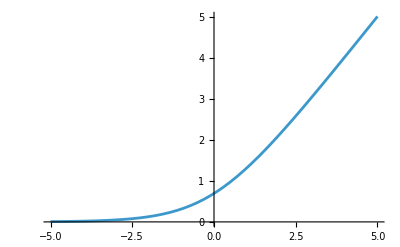

```mathematica
Plot[Log[b]/.p->1/.s1,{x,-5,5}]
```

```mathematica
yy1=FullSimplify[Log[b]/.s1]
```

Log[(ⅇ^x (1+ⅇ^x))/((1+ⅇ^x-p) p)]

```mathematica
yy2=FullSimplify[D[yy1,x]]
```

1-1/(1+ⅇ^x)+(-1+p)/(-1-ⅇ^x+p)

```mathematica
Limit[yy2,x->Infinity]
```

1

```mathematica
yy3=FullSimplify[D[Log[b],p]]
```

(-1-2 (-1+l) p)/(p+(-1+l) p^2)

```mathematica
yy3/.l->1
```

-1/p